## Inicializaciones

```mathematica
θA=π/2.;
```

## Operadores

### Funciones externas

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

### Hadamard

```mathematica
CoinH[t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],FourierMatrix[2]]
```

#### Eigenestados

```mathematica
VecsCoinH=Normalize/@Eigenvectors[FourierMatrix[2]]//N
```

{{-0.382683,0.92388},{0.92388,0.382683}}

```mathematica
psiH1=VecsCoinH[[1]]
```

{-0.382683,0.92388}

```mathematica
psiH2=VecsCoinH[[2]]
```

{0.92388,0.382683}

### Coin A

```mathematica
expCoinA={{Cos[θA/2.],-Sin[θA/2.]},{Sin[θA/2.],Cos[θA/2.]}};
```

```mathematica
CoinA[t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoinA]]
```

#### Eigenestados

```mathematica
VecsCoinA=Normalize/@Eigenvectors[expCoinA]
```

{{0.707107+0. ⅈ,0.-0.707107 ⅈ},{0.707107+0. ⅈ,0.+0.707107 ⅈ}}

```mathematica
psiA1=VecsCoinA[[1]]
```

{0.707107+0. ⅈ,0.-0.707107 ⅈ}

```mathematica
psiA2=VecsCoinA[[2]]
```

{0.707107+0. ⅈ,0.+0.707107 ⅈ}

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

### Unitaria

```mathematica
Unitary[t_Integer,coin_]:=Shift[t].coin[t]
```

## Funciones cálculos

### Estado final de la caminata después de t pasos

```mathematica
DQWL[ψ0_,t_Integer,coin_]:=
Module[{psi},
psi=ψ0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[i,coin]],{i,t}];
psi
]
```

```mathematica
psifH1=DQWL[psiH1,1,CoinH]
```

{0,-0.92388,0,0,0.382683,0}

```mathematica
psifH2=DQWL[psiH1,2,CoinH]
```

{0,0.653281,0,0,-0.653281,0.270598,0,0,0.270598,0}

```mathematica
psifA2=DQWL[psiA1,2,CoinA]
```

{0,0.353553-0.353553 ⅈ,0,0,-0.353553+0.353553 ⅈ,0.353553+0.353553 ⅈ,0,0,0.353553+0.353553 ⅈ,0}

### Matriz de densidad reducida de la moneda

#### MatrixPartialTrace

```mathematica
MatrixPartialTrace[{psifH1}ᵀ.Conjugate[{psifH1}],1,{3,2}]
```

{{0.146447,0.},{0.,0.853553}}

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

```mathematica
PosProbDistrib[psifA2,2]
```

{0.25,0,0.5,0,0.25}

### Matriz de densidad reducida de la moneda

```mathematica
ClearAll@ReducedCoinMatrices
```

```mathematica
ReducedCoinMatrices[ψ0_,t_Integer,coin_]:=
Module[{psi,reducedMatrix},
psi=ψ0;
Table[
reducedMatrix=MatrixPartialTrace[{#}ᵀ.Conjugate[{#}]&[psi],1,{2(i-1)+1,2}];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[i,coin]];
reducedMatrix,{i,t+1}
]
]
```

```mathematica
ReducedCoinMatrices[psiH1,3,CoinH]//Column
```

{{0.146447,-0.353553},{-0.353553,0.853553}}
{{0.146447,0.},{0.,0.853553}}
{{0.5,-0.176777},{-0.176777,0.5}}
{{0.323223,-0.353553},{-0.353553,0.676777}}

```mathematica
ReducedCoinMatrices[psiA1,3,CoinA]//Column
```

{{0.5+0. ⅈ,0.+0.5 ⅈ},{0.-0.5 ⅈ,0.5+0. ⅈ}}
{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.5+0. ⅈ}}
{{0.5+0. ⅈ,0.+0.25 ⅈ},{0.-0.25 ⅈ,0.5+0. ⅈ}}
{{0.5+0. ⅈ,0.+0.25 ⅈ},{0.-0.25 ⅈ,0.5+0. ⅈ}}

#### Revisando el código

```mathematica
psi0=ArrayPad[psiH1,2]
```

{0,0,-0.382683,0.92388,0,0}

t=0

```mathematica
MatrixPartialTrace[{psi0[[3;;-3]]}ᵀ.Conjugate[{psi0[[3;;-3]]}],1,{2(1-1)+1,2}]
```

{{0.146447,-0.353553},{-0.353553,0.853553}}

```mathematica
psi1=ArrayPad[Chop[#.psi0]&[Unitary[1,CoinH]],2]
```

{0,0,0,-0.92388,0,0,0.382683,0,0,0}

t=1

```mathematica
MatrixPartialTrace[{psi1[[3;;-3]]}ᵀ.Conjugate[{psi1[[3;;-3]]}],1,{2(2-1)+1,2}]
```

{{0.146447,0.},{0.,0.853553}}

```mathematica
psi2=ArrayPad[Chop[#.psi1]&[Unitary[2,CoinH]],2]
```

{0,0,0,0.653281,0,0,-0.653281,0.270598,0,0,0.270598,0,0,0}

t=2

```mathematica
MatrixPartialTrace[{psi2[[3;;-3]]}ᵀ.Conjugate[{psi2[[3;;-3]]}],1,{2(3-1)+1,2}]
```

{{0.5,-0.176777},{-0.176777,0.5}}

```mathematica
psi3=ArrayPad[Chop[#.psi2]&[Unitary[3,CoinH]],2]
```

{0,0,0,-0.46194,0,0,0.46194,-0.653281,0,0,-0.270598,0.191342,0,0,0.191342,0,0,0}

t=3

```mathematica
MatrixPartialTrace[{psi3[[3;;-3]]}ᵀ.Conjugate[{psi3[[3;;-3]]}],1,{2(4-1)+1,2}]
```

{{0.323223,-0.353553},{-0.353553,0.676777}}

```mathematica
psi4=ArrayPad[Chop[#.psi3]&[Unitary[4,CoinH]],2]
```

{0,0,0,0.326641,0,0,-0.326641,0.788581,0,0,-0.135299,-0.326641,0,0,-0.0560427,0.135299,0,0,0.135299,0,0,0}

### Probabilidad de ir hacia la izquirda o derecha vs. el tiempo

```mathematica
PlotRightProb[ψ0_,t_Integer,coin_]:=
ListLinePlot[{Range[0,t],ReducedCoinMatrices[ψ0,t,coin][[All,1,1]]}ᵀ,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"","Probabilidad de ir a la derecha"}),
FrameTicksStyle->13
]
```

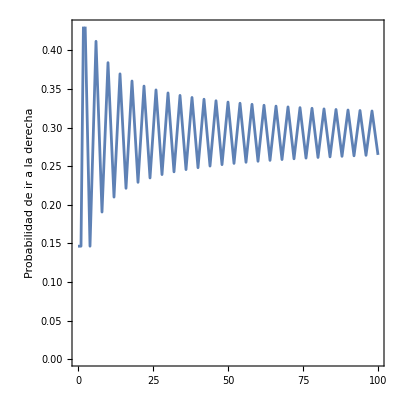

```mathematica
PlotRightProb[psiH1,100,CoinH]
```

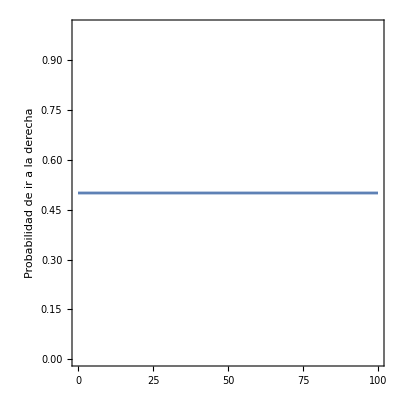

```mathematica
PlotRightProb[psiA1,100,CoinA]
```

```mathematica
PlotLeftProb[ψ0_,t_Integer,coin_]:=
ListLinePlot[{Range[0,t],ReducedCoinMatrices[ψ0,t,coin][[All,2,2]]}ᵀ,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"","Probabilidad de ir a la izquierda"}),
FrameTicksStyle->13
]
```

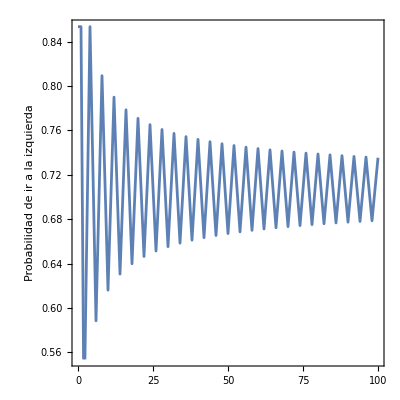

```mathematica
PlotLeftProb[psiH1,100,CoinH]
```

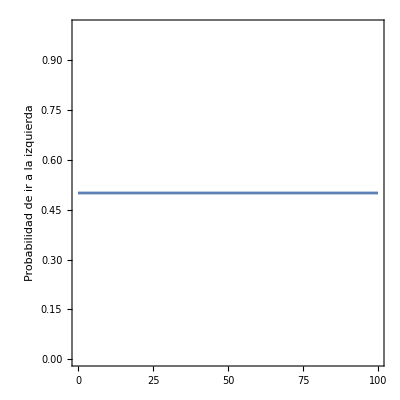

```mathematica
PlotLeftProb[psiA1,100,CoinA]
```